Linear Coupling

```mathematica
<<Notation`
```

```mathematica
Notation[(x_)^* ⟺ Conjugate[(x_)]]
```

```mathematica
δ[i_,j_]:=KroneckerDelta[i,j]
```

```mathematica
RHSfunc[n_]:=-(κ[n]/2+ⅈ×Δ[n])a[n]+ⅈ J1*(δ[n,1]*a[2]+δ[n,2]*a[1])+ⅈ J3*(δ[n,2]*a[3]+δ[n,3]*a[2])+δ[n,1]*s
```

```mathematica
(*LHSfunc[n_]:=D[a[n][t].00,t]*)
```

```mathematica
RHSfunc[1]
RHSfunc[2]
RHSfunc[3]
```

s+ⅈ J1 a[2]+a[1] (-ⅈ Δ[1]-κ[1]/2)

ⅈ J1 a[1]+ⅈ J3 a[3]+a[2] (-ⅈ Δ[2]-κ[2]/2)

ⅈ J3 a[2]+a[3] (-ⅈ Δ[3]-κ[3]/2)

```mathematica
(*Coefs = CoefficientArrays[{RHSfunc[1], RHSfunc[2], RHSfunc[3]},{a[1],a[2],a[3]}]*)
```

```mathematica
M = {{-I×κ[1]/2+Δ[1],-J1,0},{-J1,-I×κ[2]/2+Δ[2],-J3},{0,-J3,-I×κ[3]/2+Δ[3]}};
```

```mathematica
M//MatrixForm
```

(Δ[1]-1/2 ⅈ κ[1] | -J1 | 0
-J1 | Δ[2]-1/2 ⅈ κ[2] | -J3
0 | -J3 | Δ[3]-1/2 ⅈ κ[3])

```mathematica
ωbAS=Re[Eigenvalues[M][[1]]];
ωbC=Re[Eigenvalues[M][[2]]];
ωbS=Re[Eigenvalues[M][[3]]];
```

```mathematica
rnum={Δ[1]->0,Δ[2]->0,Δ[3]->0,κ[1]->1,κ[2]->1,κ[3]-> 1,J1->J,J3->J};
```

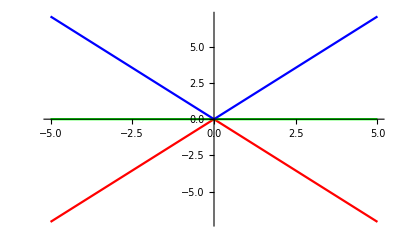

```mathematica
Plot[{ωbAS,ωbC,ωbS}/.rnum//Evaluate,{J,-5,5},PlotStyle->{Red,Green,Blue}](*,{Gray,Dashed}}]*)
```

```mathematica
rnum={Δ[1]->0,Δ[2]->0,Δ[3]->0,κ[1]->1,κ[2]->5,κ[3]-> 1,J1->J,J3->J};
```

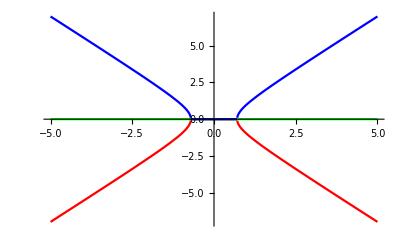

```mathematica
Plot[{ωbAS,ωbC,ωbS}/.rnum//Evaluate,{J,-5,5},PlotStyle->{Red,Green,Blue}](*,{Gray,Dashed}}]*)
```

```mathematica
Solutions = Solve[{RHSfunc[1]==0, RHSfunc[2]==0, RHSfunc[3]==0},{a[1],a[2],a[3]}];
```

```mathematica
E1 = (s (-J3^2-(-ⅈ Δ[2]-κ[2]/2) (-ⅈ Δ[3]-κ[3]/2)))/(-((-ⅈ Δ[1]-κ[1]/2) (-J3^2-(-ⅈ Δ[2]-κ[2]/2) (-ⅈ Δ[3]-κ[3]/2)))+J1^2 (-ⅈ Δ[3]-κ[3]/2))×Conjugate[(s (-J3^2-(-ⅈ Δ[2]-κ[2]/2) (-ⅈ Δ[3]-κ[3]/2)))/(-((-ⅈ Δ[1]-κ[1]/2) (-J3^2-(-ⅈ Δ[2]-κ[2]/2) (-ⅈ Δ[3]-κ[3]/2)))+J1^2 (-ⅈ Δ[3]-κ[3]/2))]//Simplify;
```

```mathematica
E2 = (4 ⅈ J1 s (2 Δ[3]-ⅈ κ[3]))/(8 J3^2 Δ[1]+8 J1^2 Δ[3]-8 Δ[1] Δ[2] Δ[3]-4 ⅈ J3^2 κ[1]+4 ⅈ Δ[2] Δ[3] κ[1]+4 ⅈ Δ[1] Δ[3] κ[2]+2 Δ[3] κ[1] κ[2]-4 ⅈ J1^2 κ[3]+4 ⅈ Δ[1] Δ[2] κ[3]+2 Δ[2] κ[1] κ[3]+2 Δ[1] κ[2] κ[3]-ⅈ κ[1] κ[2] κ[3])*Conjugate[(4 ⅈ J1 s (2 Δ[3]-ⅈ κ[3]))/(8 J3^2 Δ[1]+8 J1^2 Δ[3]-8 Δ[1] Δ[2] Δ[3]-4 ⅈ J3^2 κ[1]+4 ⅈ Δ[2] Δ[3] κ[1]+4 ⅈ Δ[1] Δ[3] κ[2]+2 Δ[3] κ[1] κ[2]-4 ⅈ J1^2 κ[3]+4 ⅈ Δ[1] Δ[2] κ[3]+2 Δ[2] κ[1] κ[3]+2 Δ[1] κ[2] κ[3]-ⅈ κ[1] κ[2] κ[3])]//Simplify;
```

```mathematica
E3 = (8 ⅈ J1 J3 s)/(8 J3^2 Δ[1]+8 J1^2 Δ[3]-8 Δ[1] Δ[2] Δ[3]-4 ⅈ J3^2 κ[1]+4 ⅈ Δ[2] Δ[3] κ[1]+4 ⅈ Δ[1] Δ[3] κ[2]+2 Δ[3] κ[1] κ[2]-4 ⅈ J1^2 κ[3]+4 ⅈ Δ[1] Δ[2] κ[3]+2 Δ[2] κ[1] κ[3]+2 Δ[1] κ[2] κ[3]-ⅈ κ[1] κ[2] κ[3])*Conjugate[(8 ⅈ J1 J3 s)/(8 J3^2 Δ[1]+8 J1^2 Δ[3]-8 Δ[1] Δ[2] Δ[3]-4 ⅈ J3^2 κ[1]+4 ⅈ Δ[2] Δ[3] κ[1]+4 ⅈ Δ[1] Δ[3] κ[2]+2 Δ[3] κ[1] κ[2]-4 ⅈ J1^2 κ[3]+4 ⅈ Δ[1] Δ[2] κ[3]+2 Δ[2] κ[1] κ[3]+2 Δ[1] κ[2] κ[3]-ⅈ κ[1] κ[2] κ[3])]//Simplify;
```

```mathematica
rnum={Δ[1]->δ,Δ[2]->δ,Δ[3]->δ,κ[1]->1,κ[2]->1,κ[3]-> 1,J1->3,J3->3, s->1};
```

```mathematica
EachEnergy = Plot[{E1,E2,E3}/.rnum//Evaluate,{δ,-10,10},PlotStyle->{Red,Green,Blue},PlotRange->All];
```

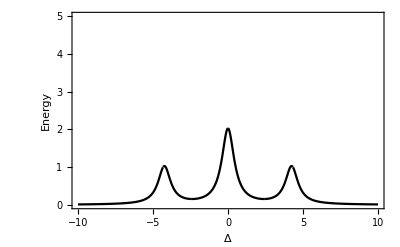

```mathematica
SumEnergy = Plot[E1+E2+E3/.rnum//Evaluate,{δ,-10,10},PlotStyle->{Black},PlotRange->{{-10,10}, {0,5}}, Frame->True,FrameLabel->{Style["Δ"],Style["Energy"]},FrameStyle->Directive[Black,14]]
```

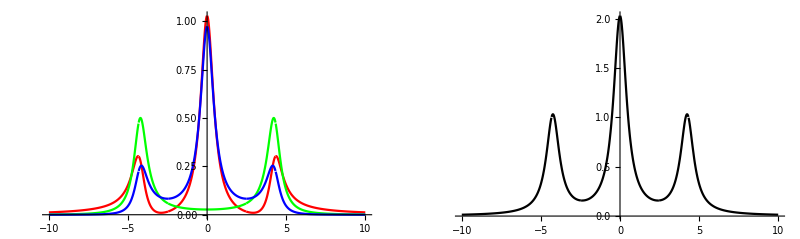

```mathematica
GraphicsGrid[{{EachEnergy, SumEnergy}}]
```

```mathematica
rnum={Δ[1]->δ,Δ[2]->δ,Δ[3]->δ,κ[1]->1,κ[2]->1,κ[3]-> 1,J1->J,J3->J, s->1};
```

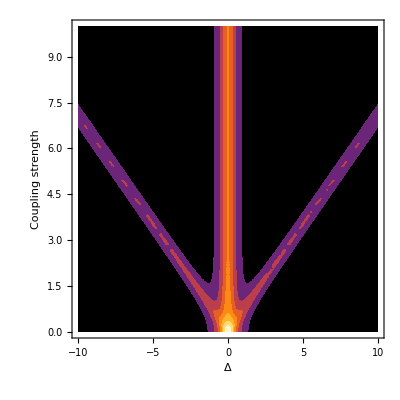

```mathematica
ContourPlot[E1+E2+E3/.rnum, {δ,-10,10},{J,0,10},PlotRange->All, ContourStyle->None, ColorFunction->"SunsetColors", Frame->True,FrameLabel->{Style["Δ"],Style["Coupling strength"]},FrameStyle->Directive[Black,14]]
```

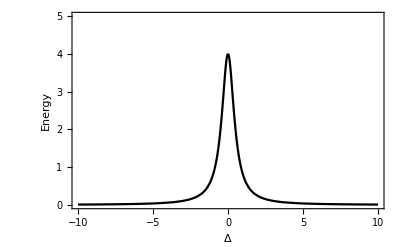

```mathematica
rnum={Δ[1]->δ,Δ[2]->δ,Δ[3]->δ,κ[1]->1,κ[2]->1,κ[3]-> 1,J1->0,J3->0, s->1};
Plot[E1+E2+E3/.rnum//Evaluate,{δ,-10,10},PlotStyle->{Black},PlotRange->{{-10,10}, {0,5}}, Frame->True,FrameLabel->{Style["Δ"],Style["Energy"]},FrameStyle->Directive[Black,14]]
```

```mathematica
rnum={Δ[1]->δ,Δ[2]->δ,Δ[3]->δ,κ[1]->1,κ[2]->1,κ[3]-> 1,J1->J,J3->J, s->1};
```

```mathematica
gif=Table[Plot[E1+E2+E3/.rnum,{δ,-10,10},PlotStyle->{Black},PlotRange->{{-10,10}, {0,5}}, Frame->True,FrameLabel->{Style["Δ"],Style["Energy"]},FrameStyle->Directive[Black,14]],{J,0,5,0.01}];
```

```mathematica
Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\uploads\\Luca\\Talks\\EQD\\evolution.gif",gif,"DisplayDurations"->0.015]
```

G:\.shortcut-targets-by-id\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\LPD Team\uploads\Luca\Talks\EQD\evolution.gif

```mathematica
rnum={Δ[1]->δ,Δ[2]->δ,Δ[3]->δ+10,κ[1]->1,κ[2]->1,κ[3]-> 1,J1->J,J3->J, s->1};
```

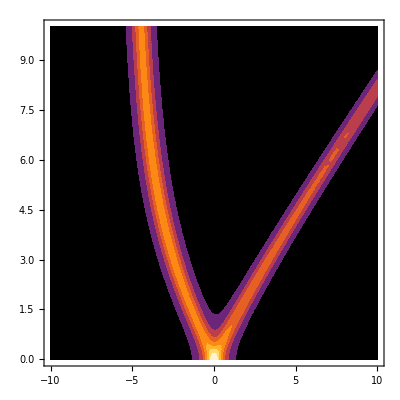

```mathematica
ContourPlot[E1+E2+E3/.rnum, {δ,-10,10},{J,0,10},PlotRange->All, ContourStyle->None, ColorFunction->"SunsetColors"]
```

Nonlinear Coupling

```mathematica
RHSfunc[n_]:=-(κ[n]/2+ⅈ×Δ[n])a[n]+ⅈ J1*(δ[n,1]*a[2]+δ[n,2]*a[1])+ⅈ J3*(δ[n,2]*a[3]+δ[n,3]*a[2])+I×Abs[a[n]×SuperStar[a[n]]]×a[n]+δ[n,1]*s
```

```mathematica
RHSfunc[1]
RHSfunc[2]
RHSfunc[3]
```

s+ⅈ J1 a[2]+ⅈ a[1] Abs[a[1] a[1]^*]+a[1] (-ⅈ Δ[1]-κ[1]/2)

ⅈ J1 a[1]+ⅈ J3 a[3]+ⅈ a[2] Abs[a[2] a[2]^*]+a[2] (-ⅈ Δ[2]-κ[2]/2)

ⅈ J3 a[2]+ⅈ a[3] Abs[a[3] a[3]^*]+a[3] (-ⅈ Δ[3]-κ[3]/2)